run complete

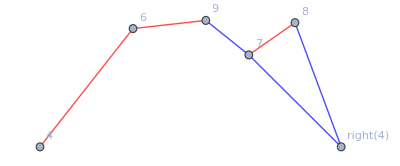
<|Chain→-Graphics-,Parastichy→<|RGBColor[0, 0, 1]→2,RGBColor[1, 0, 0]→2|>,MeanZ→2.61457,MeanRadius→0.161849|>

```mathematica
Get["CoinStackingCode.m",Path->{PersistentSymbol["persistentGitHubPath","Local"]}];
run=doRunScale[<|"rSlope"->0.23,"diskMax"->8|>];
```

```mathematica
newSupportDisks
```

{8→Disk[{0.346572,2.79169},0.0922179],left[8]→Disk[{-0.653428,2.79169},0.0922179],4→Disk[{-0.5,2.39658},0.331628],right[4]→Disk[{0.5,2.39658},0.331628],6→Disk[{-0.191241,2.77297},0.155193],5→Disk[{5.55112×10^-17,2.49916},0.178785],7→Disk[{0.193289,2.68912},0.0922179]}

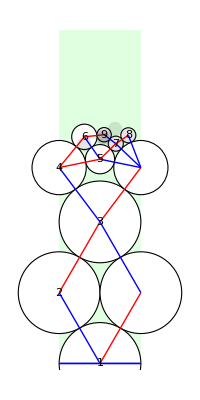

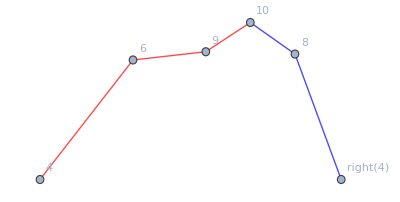
<|Chain→-Graphics-,Parastichy→<|RGBColor[0, 0, 1]→2,RGBColor[1, 0, 0]→3|>,MeanZ→2.64977,MeanRadius→0.150641|>

run complete

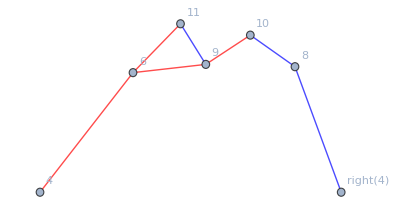
<|Chain→-Graphics-,Parastichy→<|RGBColor[0, 0, 1]→2,RGBColor[1, 0, 0]→3|>,MeanZ→2.70025,MeanRadius→0.134261|>

```mathematica
globalRun=run;


Select[newSupportTable,!MissingQ[#NextDisk]&];
newSupportTable = Select[newSupportTable,isLeftRightSupported];
newSupportTable = Select[newSupportTable,diskIsNormalised[#NextDisk]&];
newdisksToCheckIntersection=Association[newSupportDisks];
*)(* the centre of the new disk must be above the line trhrough the centres of the support *) 

(*supportLine =  SortBy[Values@Map[diskXZ,newdisksToCheckIntersection],First];
supportLineFunction = Interpolation[supportLine,InterpolationOrder->1];
diskAboveSupportLineQ[disk_]:= diskZ[disk] > supportLineFunction[diskX[disk]];

newSupportTable = Select[newSupportTable,diskAboveSupportLineQ[#NextDisk]&];
*)(*newSupportTable= Map[newsupportTableFindIntersections[#,nextR,newdisksToCheckIntersection]&,newSupportTable];
newSupportTable= Select[newSupportTable,Length[#Intersection]==0&]
*)Show[{showRun[globalRun],
Graphics[
{
FaceForm[Opacity[0.1]],DeleteMissing[Map[#NextDisk&,monitornewSupportTable]]
}
]
},PlotRange->{Automatic,{0,4}}]
```

```mathematica
DeleteMissing[Map[#NextDisk&,monitornewSupportTable]]
```

{Disk[{0.338164,2.94875},0.065068],Disk[{0.0596284,2.9516},0.065068],Disk[{0.197394,2.84153},0.065068],Disk[{-0.0335416,2.92674},0.065068]}

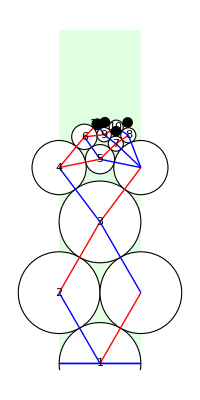

```mathematica
Show[{showRun[globalRun],
Graphics[DeleteMissing[Map[#NextDisk&,monitornewSupportTable]]]},PlotRange->{Automatic,{0,4}}]
```

```mathematica
earlierVectorsFromNode[run["ContactGraph"],9]
```

<|9->6→{-0.24461,-0.124135},9->8→{0.236794,0.0124741}|>

```mathematica
vfn
```

<|8->5→{-0.136596,-0.332312},8->7→{0.189813,-0.182156},8->9→{-0.236794,-0.0124741},8->12→{0.154433,0.149067},8->13→{-0.147952,0.147335},8->15→{-0.00691352,0.207497}|>

```mathematica
Map[keyEarlier,Keys[vfn]]
```

{True,True,False,False,False,False}

```mathematica
globalRun=run;
nextR=nextRadius[];
row=newFindNextDiskFromSupportSet[nextR]
```

<|Disk1→Disk[{0.0873639,6.09918},0.05],Disk2→Disk[{0.22309,6.0526},0.05],NextDiskRestsOn→{60,56},EdgeSeparation→0.0357259,NextDisk→Disk[{0.177841,6.14177},0.05],Intersection→{}|>

```mathematica
newSupportTable
```

{<|Disk1→Disk[{-0.194849,6.14076},0.05],Disk2→Disk[{-0.0824322,5.99022},0.0518062],NextDiskRestsOn→{64,50},EdgeSeparation→0.0106102,NextDisk→Disk[{-0.109713,6.08831},0.05]|>,<|Disk1→Disk[{-0.194849,6.14076},0.05],Disk2→Disk[{-0.280936,5.97902},0.0534374],NextDiskRestsOn→{64,47},EdgeSeparation→-0.0173501,NextDisk→Disk[{-0.276003,6.08234},0.05]|>,<|Disk1→Disk[{-0.109713,6.08831},0.05],Disk2→Disk[{0.00194314,6.04719},0.05],NextDiskRestsOn→{59,54},EdgeSeparation→0.0116557,NextDisk→Disk[{-0.02611,6.14318},0.05]|>,<|Disk1→Disk[{-0.109713,6.08831},0.05],Disk2→Disk[{0.0873639,6.09918},0.05],NextDiskRestsOn→{59,60},EdgeSeparation→0.0970764,NextDisk→Disk[{-0.0120641,6.10987},0.05]|>,<|Disk1→Disk[{-0.109713,6.08831},0.05],Disk2→Disk[{-0.280936,5.97902},0.0534374],NextDiskRestsOn→{59,47},EdgeSeparation→0.0677859,NextDisk→Disk[{-0.19688,6.0393},0.05]|>,<|Disk1→Disk[{-0.109713,6.08831},0.05],Disk2→Disk[{-0.276003,6.08234},0.05],NextDiskRestsOn→{59,58},EdgeSeparation→0.0662905,NextDisk→Disk[{-0.194849,6.14076},0.05]|>,<|Disk1→Disk[{-0.0824322,5.99022},0.0518062],Disk2→Disk[{0.0873639,6.09918},0.05],NextDiskRestsOn→{50,60},EdgeSeparation→0.0679898,NextDisk→Disk[{0.00194314,6.04719},0.05]|>,<|Disk1→Disk[{-0.0824322,5.99022},0.0518062],Disk2→Disk[{-0.280936,5.97902},0.0534374],NextDiskRestsOn→{50,47},EdgeSeparation→0.0932601,NextDisk→Disk[{-0.182279,6.0101},0.05]|>,<|Disk1→Disk[{0.00194314,6.04719},0.05],Disk2→Disk[{0.132204,6.00882},0.0508799],NextDiskRestsOn→{54,51},EdgeSeparation→0.0293812,NextDisk→Disk[{0.0873639,6.09918},0.05]|>,<|Disk1→Disk[{0.0873639,6.09918},0.05],Disk2→Disk[{0.22309,6.0526},0.05],NextDiskRestsOn→{60,56},EdgeSeparation→0.0357259,NextDisk→Disk[{0.177841,6.14177},0.05]|>,<|Disk1→Disk[{0.132204,6.00882},0.0508799],Disk2→Disk[{0.22309,6.0526},0.05],NextDiskRestsOn→{51,56},EdgeSeparation→-0.00999435,NextDisk→Disk[{0.140745,6.10934},0.05]|>,<|Disk1→Disk[{0.132204,6.00882},0.0508799],Disk2→Disk[{0.296875,6.12009},0.05],NextDiskRestsOn→{51,62},EdgeSeparation→0.0637907,NextDisk→Disk[{0.206726,6.07681},0.05]|>,<|Disk1→Disk[{0.22309,6.0526},0.05],Disk2→Disk[{0.366164,6.04799},0.05],NextDiskRestsOn→{56,55},EdgeSeparation→0.0430738,NextDisk→Disk[{0.296875,6.12009},0.05]|>,<|Disk1→Disk[{0.296875,6.12009},0.05],Disk2→Disk[{0.406762,6.13938},0.05],NextDiskRestsOn→{62,63},EdgeSeparation→0.00988763,NextDisk→Disk[{0.337474,6.21148},0.05]|>,<|Disk1→Disk[{0.296875,6.12009},0.05],Disk2→Disk[{0.465607,6.05852},0.05],NextDiskRestsOn→{62,57},EdgeSeparation→0.0687324,NextDisk→Disk[{0.396318,6.13063},0.05]|>,<|Disk1→Disk[{0.366164,6.04799},0.05],Disk2→Disk[{0.465607,6.05852},0.05],NextDiskRestsOn→{55,57},EdgeSeparation→-0.000556401,NextDisk→Disk[{0.406762,6.13938},0.05]|>,<|Disk1→Disk[{0.366164,6.04799},0.05],Disk2→Disk[{0.556864,6.09942},0.05],NextDiskRestsOn→{55,right[61]},EdgeSeparation→0.0907004,NextDisk→Disk[{0.45742,6.08888},0.05]|>,<|Disk1→Disk[{0.406762,6.13938},0.05],Disk2→Disk[{0.556864,6.09942},0.05],NextDiskRestsOn→{63,right[61]},EdgeSeparation→0.0501015,NextDisk→Disk[{0.498019,6.18027},0.05]|>,<|Disk1→Disk[{0.465607,6.05852},0.05],Disk2→Disk[{0.556864,6.09942},0.05],NextDiskRestsOn→{57,right[61]},EdgeSeparation→-0.00874321,NextDisk→Disk[{0.475822,6.158},0.05]|>,<|Disk1→Disk[{-0.534393,6.05852},0.05],Disk2→Disk[{-0.370614,6.03056},0.05],NextDiskRestsOn→{left[57],53},EdgeSeparation→0.0637789,NextDisk→Disk[{-0.443136,6.09942},0.05]|>,<|Disk1→Disk[{-0.443136,6.09942},0.05],Disk2→Disk[{-0.280936,5.97902},0.0534374],NextDiskRestsOn→{61,47},EdgeSeparation→0.0587626,NextDisk→Disk[{-0.356238,6.04993},0.05]|>,<|Disk1→Disk[{-0.443136,6.09942},0.05],Disk2→Disk[{-0.276003,6.08234},0.05],NextDiskRestsOn→{61,58},EdgeSeparation→0.0671329,NextDisk→Disk[{-0.354054,6.14485},0.05]|>,<|Disk1→Disk[{-0.370614,6.03056},0.05],Disk2→Disk[{-0.280936,5.97902},0.0534374],NextDiskRestsOn→{53,47},EdgeSeparation→-0.0137595,NextDisk→Disk[{-0.28508,6.08237},0.05]|>,<|Disk1→Disk[{-0.370614,6.03056},0.05],Disk2→Disk[{-0.276003,6.08234},0.05],NextDiskRestsOn→{53,58},EdgeSeparation→-0.00538922,NextDisk→Disk[{-0.363735,6.13033},0.05]|>}

```mathematica
data = SortBy[Values@Map[diskXZ,newdisksToCheckIntersection],First]
```

{{-0.593238,6.13938},{-0.534393,6.05852},{-0.443136,6.09942},{-0.370614,6.03056},{-0.280936,5.97902},{-0.276003,6.08234},{-0.194849,6.14076},{-0.109713,6.08831},{-0.0824322,5.99022},{0.00194314,6.04719},{0.0873639,6.09918},{0.132204,6.00882},{0.22309,6.0526},{0.296875,6.12009},{0.366164,6.04799},{0.406762,6.13938},{0.465607,6.05852},{0.556864,6.09942}}

```mathematica
Interpolation[data,InterpolationOrder->1][-0.182]
```

6.13285

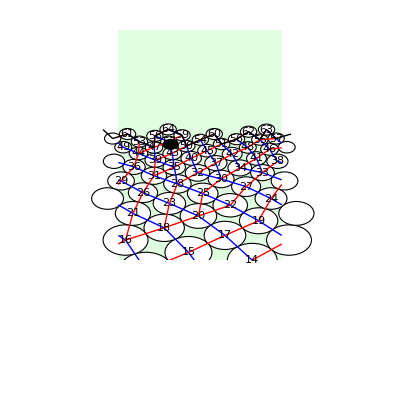

```mathematica
Show[{showRun[run],

Graphics[{{Thick,Line[data]},Disk[{-0.18227933535112356,6.01009931278059},0.05]}]},PlotRange->{Automatic,{5,7}}]
```